# Assignment 8

## Cameron Embree - W7 - 3/3/14-3/10/14

ORIGINAL

{a→-2.63563,b→0.143646,c→0.551447,d→3.22294,e→-0.432894}

-0.432894+0.551447 x-x^2+3.22294 y+0.143646 x y-2.63563 y^2

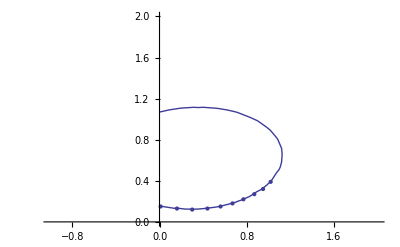

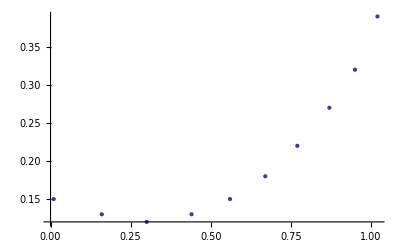

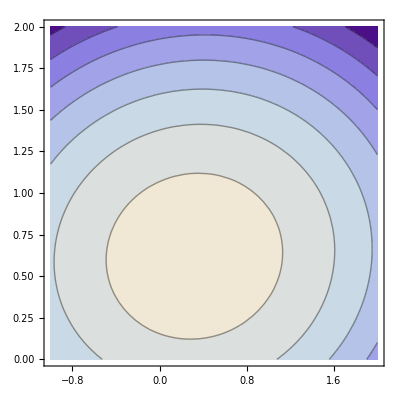

PERTURBED

{a→-1.67356,b→-0.0965675,c→0.623592,d→2.8492,e→-0.412661}

-0.412661+0.623592 x-x^2+2.8492 y-0.0965675 x y-1.67356 y^2

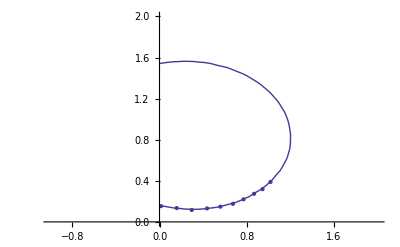

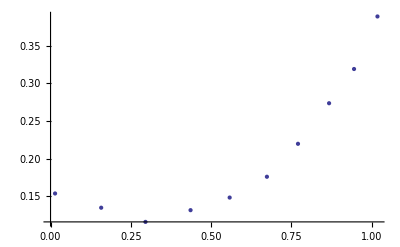

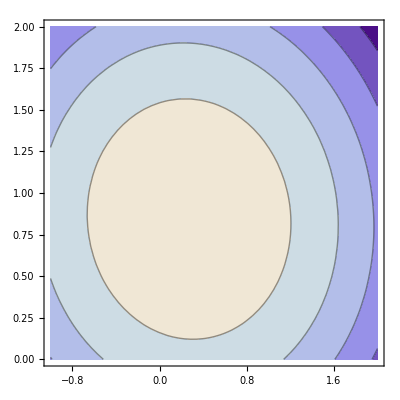

```mathematica
(* QUESTION 1 - Using Linear Least Squares,determine the orbital parameters a,b,c,d,e given the following observations (as (x,y)-coordinates).(1.02,.39),(.95,.32),(.87,.27),(.77,.22),(.67,.18),(.56,.15),(.44,.13),(.30,.12),(.16,.13),(.01,.15)
Plot the resulting orbit for the given data points. *)

(* ORIGINAL DATA *)
Print["ORIGINAL"]
Clear[b]
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
origData={{1.02,0.39,0},{0.95,0.32,0},{0.87,0.27,0},{0.77,0.22,0},{0.67,0.18,0},{0.56,0.15,0},{0.44,0.13,0},{0.30,0.12,0},{0.16,0.13,0},{0.01,0.15,0}};
origFits=FindFit[origData,model,{a,b,c,d,e},{x,y}]

origFun=model/.origFits[[All]]

Show[
ListPlot[Tooltip[origData[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[origFun==0,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[origData[[All,1;;2]]]]
ContourPlot[origFun,{x,-1,2},{y,0,2}]



(* QUESTION 2 - 2. This least squares problem is nearly rank deficient. To see what effect this has on the solution: perturb the input data slightly by adding to each coordinate of each data point a random number drawn uniformly from the interval[-.005,.005].and solve the least squares problem with the per-turbed data. Compare the new values for the parameters with those previously computed. What effect does this difference have on the plot of the orbit?Can you explain this behavior? *)

(* ANSWER: The orbit is significantly changed from small errors in the data points for the planetary trajectory. This can be seen in the values for a,b,c,d, and e from the perturbed that differ significantly from the origonal's data*)

(* PERTURBED DATA *)
Print["PERTURBED"]

perturbedData=Map[{#[[1]]+RandomReal[{-0.005,0.005}],#[[2]]+RandomReal[{-0.005,0.005}],0}&,origData];
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
perturbedFits=FindFit[perturbedData,model,{a,b,c,d,e},{x,y}]

perturbedFun=model/.perturbedFits[[All]]

Show[
ListPlot[Tooltip[perturbedData[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[perturbedFun==0,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[perturbedData[[All,1;;2]]]]
ContourPlot[perturbedFun,{x,-1,2},{y,0,2}]
```

(y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1)

{{0.1521,0.3978,1.02,0.39,1},{0.1024,0.304,0.95,0.32,1},{0.0729,0.2349,0.87,0.27,1},{0.0484,0.1694,0.77,0.22,1},{0.0324,0.1206,0.67,0.18,1},{0.0225,0.084,0.56,0.15,1},{0.0169,0.0572,0.44,0.13,1},{0.0144,0.036,0.3,0.12,1},{0.0169,0.0208,0.16,0.13,1},{0.0225,0.0015,0.01,0.15,1}}

{{-0.391819,-0.422182,0.567493,0.370256,-0.395998,-0.125416,-0.14491,-0.0502098,0.0339479,-0.109025},{-0.374959,-0.320119,0.151426,-0.0959632,0.458635,0.342581,0.379943,0.235041,0.142911,0.420783},{-0.358805,-0.223357,-0.08393,-0.319109,0.330016,-0.00310136,-0.0431995,-0.250222,-0.494607,-0.542644},{-0.340099,-0.112449,-0.262289,-0.335035,-0.0139541,-0.4688,-0.431037,-0.194854,0.17979,0.463238},{-0.322566,-0.00943903,-0.350298,-0.160304,-0.282012,-0.128495,0.206513,0.549537,0.369954,-0.4122},{-0.304646,0.0953288,-0.34536,0.0885457,-0.352895,0.730086,-0.262319,-0.185461,-0.0438336,0.0911102},{-0.286233,0.202831,-0.25723,0.328588,-0.14998,-0.276591,0.636941,-0.375748,-0.183475,0.152488},{-0.265792,0.322502,-0.0804782,0.467403,0.283483,-0.137186,-0.327636,0.494207,-0.375236,0.0939891},{-0.246579,0.436682,0.179743,0.161392,0.384883,0.037172,-0.112943,-0.329245,0.584998,-0.277951},{-0.226365,0.558335,0.481921,-0.503589,-0.262063,0.0297491,0.0986466,0.106953,-0.214449,0.120212}}

{{3.78604,0.,0.,0.,0.},{0.,0.944923,0.,0.,0.},{0.,0.,0.208913,0.,0.},{0.,0.,0.,0.0230432,0.},{0.,0.,0.,0.,0.00549953},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

{{-0.0464444,-0.0940456,0.3459,0.32502,-0.873907},{-0.134085,-0.314072,0.589862,0.552433,0.479855},{-0.518754,-0.748353,-0.402715,-0.0580564,-0.0728866},{-0.180497,-0.141754,0.608452,-0.759494,-0.0167896},{-0.823516,0.558917,0.00477136,0.0947587,0.0207492}}

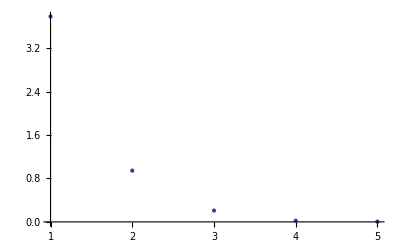

{{0.1521,0.3978,1.02,0.39,1.},{0.1024,0.304,0.95,0.32,1.},{0.0729,0.2349,0.87,0.27,1.},{0.0484,0.1694,0.77,0.22,1.},{0.0324,0.1206,0.67,0.18,1.},{0.0225,0.084,0.56,0.15,1.},{0.0169,0.0572,0.44,0.13,1.},{0.0144,0.036,0.3,0.12,1.},{0.0169,0.0208,0.16,0.13,1.},{0.0225,0.0015,0.01,0.15,1.}}

```mathematica
(* QUESTION 3 - Find the singular value decomposition for the 10×5 matrix in the original linear least squares problem.Use the singular value decomposition to compute the linear least squares problem using the first k singular values only,for k=1, . . .5. For each of the 5 solutions plot the corresponding orbit along with the given data points. *)

(* Singular Value Decomp on k values with ORIGINAL DATA *)

Clear[a,b,c,d,e,x,y]
A={{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1}}//MatrixForm
X={{a},{b},{c},{d},{e}}//MatrixForm;
B={{x^2},{x^2},{x^2},{x^2},{x^2},{x^2},{x^2},{x^2},{x^2},{x^2}}//MatrixForm;

newA=Table[A[[1,i]]/.x->origData[[All,1]][[i]]/.y->origData[[All,2]][[i]], {i,1,10}]


{u,w,v}=SingularValueDecomposition[newA];
u
w
v

ListPlot[Diagonal[w]]

u.w.Transpose[v]
```

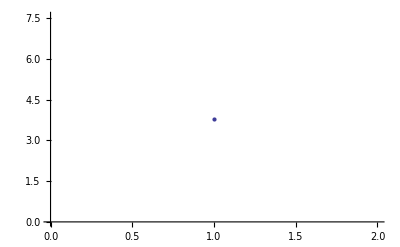

{{0.0689522,0.198396,0.768251,0.267371,1.22195},{0.0658453,0.189456,0.733635,0.255324,1.16689},{0.0631497,0.1817,0.703601,0.244871,1.11912},{0.0597467,0.171909,0.665685,0.231676,1.05881},{0.0568316,0.163521,0.633205,0.220372,1.00715},{0.053552,0.154085,0.596665,0.207655,0.949028},{0.0503147,0.14477,0.560596,0.195102,0.891658},{0.0469344,0.135044,0.522933,0.181994,0.831753},{0.0434516,0.125023,0.484129,0.168489,0.770033},{0.0399546,0.114961,0.445165,0.154929,0.708059}}

{{0.768251,0.267371,0},{0.733635,0.255324,0},{0.703601,0.244871,0},{0.665685,0.231676,0},{0.633205,0.220372,0},{0.596665,0.207655,0},{0.560596,0.195102,0},{0.522933,0.181994,0},{0.484129,0.168489,0},{0.445165,0.154929,0}}

{a→4.12807,b→1.43668,c→-7.36156×10^-16,d→-2.68472×10^-15,e→1.57988×10^-16}

1.57988×10^-16-7.36156×10^-16 x-x^2-2.68472×10^-15 y+1.43668 x y+4.12807 y^2

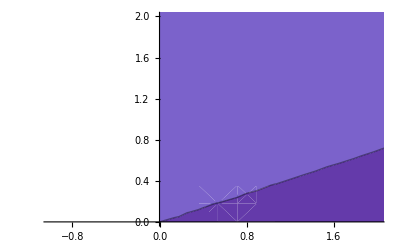

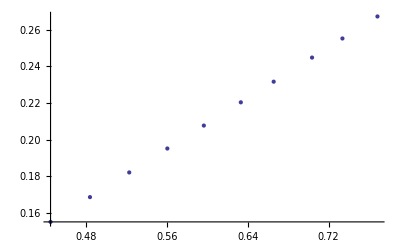

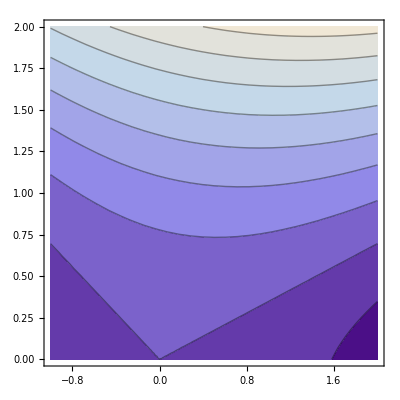

```mathematica
(* Singular Value Decomp on K=1 values with ORIGINAL DATA *)

(* K VALUE *)
kSingularValues=1;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdData31=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits31=FindFit[svdData31,model,{a,b,c,d,e},{x,y}]

svdFitFun31=model/.svdFits31[[All]]

Show[
ListPlot[Tooltip[svdData31[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun31,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdData31[[All,1;;2]]]]
ContourPlot[svdFitFun31,{x,-1,2},{y,0,2}]
```

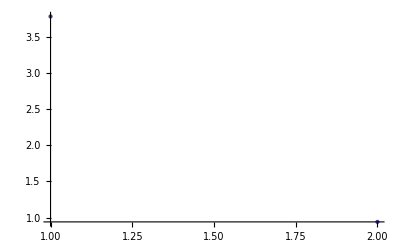

{{0.107601,0.32507,1.06744,0.325858,0.998294},{0.0946922,0.284003,0.956945,0.298977,0.999957},{0.0835975,0.248719,0.861892,0.275814,1.00079},{0.069707,0.204554,0.74279,0.246748,1.00117},{0.0579161,0.167076,0.641601,0.222013,1.00087},{0.0446876,0.125031,0.528043,0.19424,1.00032},{0.0316321,0.0835369,0.415969,0.16683,0.999769},{0.0179897,0.0401764,0.298865,0.138193,0.999247},{0.0038167,-0.00488258,0.177305,0.108511,0.999389},{-0.0105267,-0.0504941,0.0543771,0.0785367,1.00018}}

{{1.06744,0.325858,0},{0.956945,0.298977,0},{0.861892,0.275814,0},{0.74279,0.246748,0},{0.641601,0.222013,0},{0.528043,0.19424,0},{0.415969,0.16683,0},{0.298865,0.138193,0},{0.177305,0.108511,0},{0.0543771,0.0785367,0}}

{a→-2.63563,b→0.143646,c→0.551447,d→3.22294,e→-0.432894}

-0.432894+0.551447 x-x^2+3.22294 y+0.143646 x y-2.63563 y^2

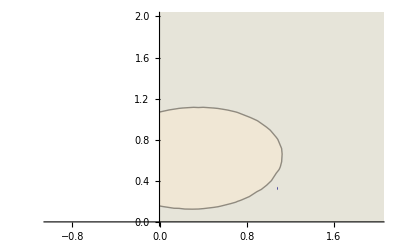

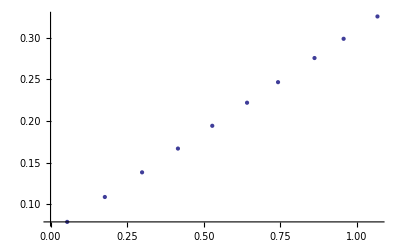

-Graphics-

```mathematica
(* Singular Value Decomp on K=2 values with ORIGINAL DATA *)

(* K VALUE *)
kSingularValues=2;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdData32=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits32=FindFit[svdData,model,{a,b,c,d,e},{x,y}]

svdFitFun32=model/.svdFits32[[All]]

Show[
ListPlot[Tooltip[svdData32[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun32,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdData32[[All,1;;2]]]]
ContourPlot[svdFitFun32,{x,-1,2},{y,0,2}]
```

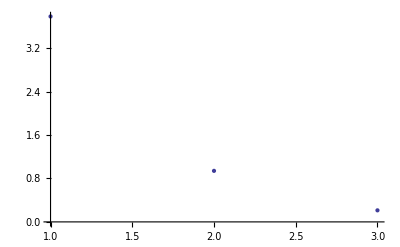

{{0.150547,0.397878,1.01722,0.400509,0.999291},{0.104141,0.300022,0.945896,0.315401,1.00018},{0.0777844,0.238864,0.86869,0.26571,1.00066},{0.0508913,0.172655,0.764794,0.214041,1.00073},{0.0303591,0.120357,0.673827,0.174111,1.00023},{0.018581,0.080771,0.558573,0.14886,0.999719},{0.0140455,0.0537213,0.436535,0.136259,0.999361},{0.0131009,0.0318881,0.304582,0.129695,0.999134},{0.0177099,0.0186714,0.161058,0.132661,0.999711},{0.0240809,0.00817838,0.0139057,0.138694,1.00098}}

{{1.01722,0.400509,0},{0.945896,0.315401,0},{0.86869,0.26571,0},{0.764794,0.214041,0},{0.673827,0.174111,0},{0.558573,0.14886,0},{0.436535,0.136259,0},{0.304582,0.129695,0},{0.161058,0.132661,0},{0.0139057,0.138694,0}}

{a→-1.21724,b→-3.0337,c→0.922373,d→5.81538,e→-0.798388}

-0.798388+0.922373 x-x^2+5.81538 y-3.0337 x y-1.21724 y^2

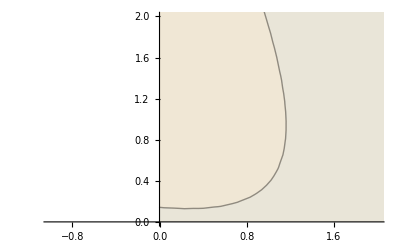

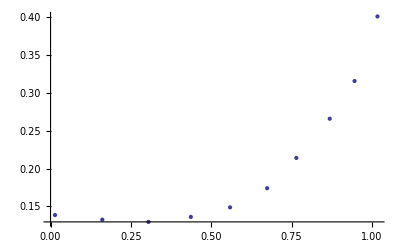

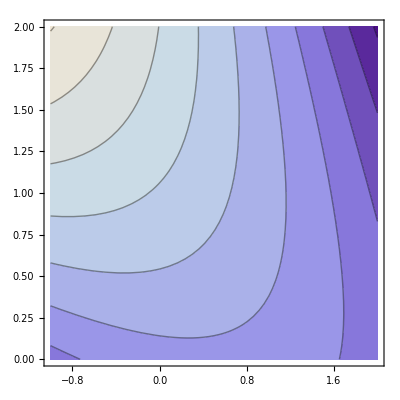

```mathematica
(* Singular Value Decomp on K=3 values with ORIGINAL DATA *)

(* K VALUE *)
kSingularValues=3;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdData33=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits33=FindFit[svdData33,model,{a,b,c,d,e},{x,y}]

svdFitFun33=model/.svdFits33[[All]]

Show[
ListPlot[Tooltip[svdData33[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun33,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdData33[[All,1;;2]]]]
ContourPlot[svdFitFun33,{x,-1,2},{y,0,2}]
```

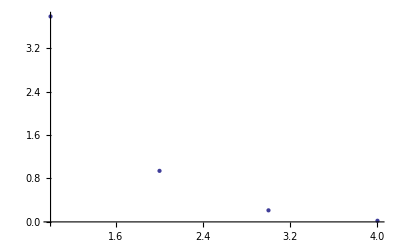

{{0.153781,0.40213,1.01681,0.394213,1.00006},{0.103067,0.298611,0.946034,0.317492,0.999922},{0.0748478,0.235003,0.869067,0.271427,0.99996},{0.0478608,0.168671,0.765183,0.219941,1.00002},{0.029562,0.119309,0.673929,0.175663,1.00004},{0.0199657,0.0825913,0.558396,0.146164,1.00005},{0.0167939,0.0573343,0.436183,0.130909,1.00001},{0.0165594,0.0364346,0.304139,0.122961,0.999952},{0.0187031,0.0199771,0.16093,0.130727,0.999947},{0.0201159,0.00296601,0.0144141,0.146414,1.00004}}

{{1.01681,0.394213,0},{0.946034,0.317492,0},{0.869067,0.271427,0},{0.765183,0.219941,0},{0.673929,0.175663,0},{0.558396,0.146164,0},{0.436183,0.130909,0},{0.304139,0.122961,0},{0.16093,0.130727,0},{0.0144141,0.146414,0}}

{a→-1.66907,b→-0.772686,c→0.684457,d→3.58171,e→-0.501524}

-0.501524+0.684457 x-x^2+3.58171 y-0.772686 x y-1.66907 y^2

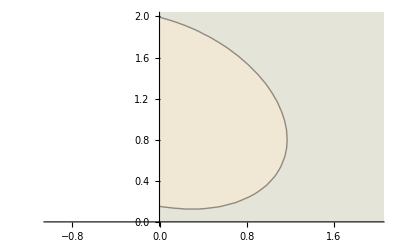

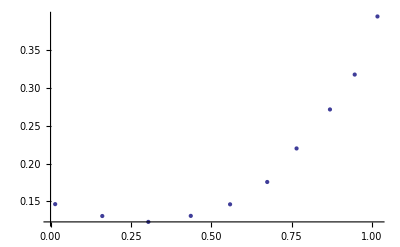

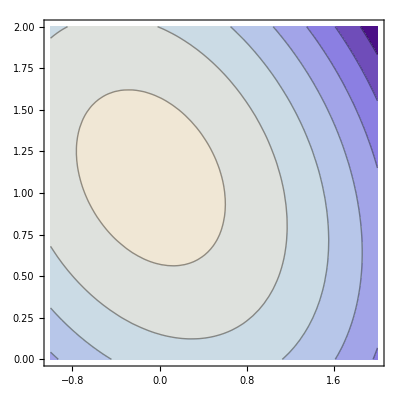

```mathematica
(* Singular Value Decomp on K=4 values with ORIGINAL DATA *)

(* NOTE: THIS ONE IS PRETTY GOOD! *)

(* K VALUE *)
kSingularValues=4;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdData34=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits34=FindFit[svdData34,model,{a,b,c,d,e},{x,y}]

svdFitFun34=model/.svdFits34[[All]]

Show[
ListPlot[Tooltip[svdData34[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun34,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdData34[[All,1;;2]]]]
ContourPlot[svdFitFun34,{x,-1,2},{y,0,2}]
```

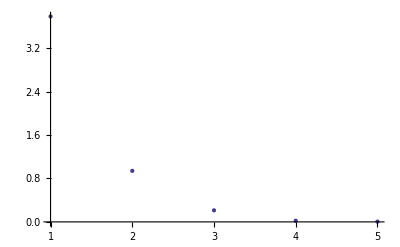

{{0.155524,0.401055,1.01696,0.394365,1.},{0.100668,0.30009,0.945816,0.317282,1.},{0.073614,0.235764,0.868955,0.271319,1.},{0.0483947,0.168342,0.765231,0.219988,1.},{0.0308986,0.118485,0.67405,0.17578,1.},{0.0214007,0.0817065,0.558526,0.14629,1.},{0.0171451,0.0571177,0.436215,0.130939,1.},{0.0150879,0.0373419,0.304006,0.122833,1.},{0.0170519,0.0209952,0.160781,0.130583,1.},{0.0214717,0.00213012,0.0145369,0.146532,1.}}

{{1.01696,0.394365,0},{0.945816,0.317282,0},{0.868955,0.271319,0},{0.765231,0.219988,0},{0.67405,0.17578,0},{0.558526,0.14629,0},{0.436215,0.130939,0},{0.304006,0.122833,0},{0.160781,0.130583,0},{0.0145369,0.146532,0}}

{a→-1.74861,b→-0.712893,c→0.675912,d→3.56392,e→-0.497479}

-0.497479+0.675912 x-x^2+3.56392 y-0.712893 x y-1.74861 y^2

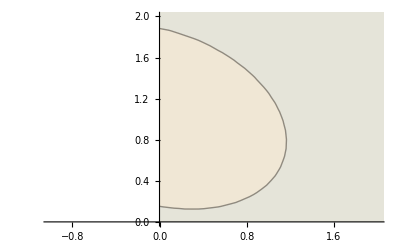

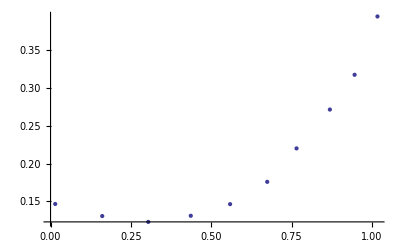

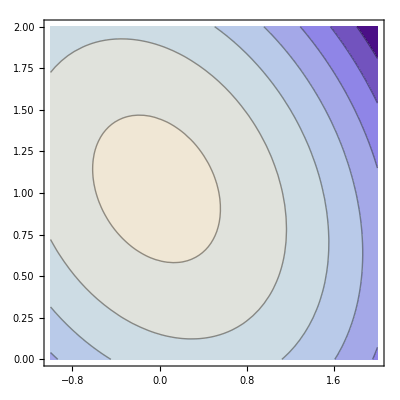

```mathematica
(* Singular Value Decomp on K=5 values with ORIGINAL DATA *)

(* K VALUE *)
kSingularValues=5;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdData35=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits35=FindFit[svdData35,model,{a,b,c,d,e},{x,y}]

svdFitFun35=model/.svdFits35[[All]]

Show[
ListPlot[Tooltip[svdData35[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun35,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdData35[[All,1;;2]]]]
ContourPlot[svdFitFun35,{x,-1,2},{y,0,2}]
```

```mathematica
(* QUESTION 4 - Perturb the input data again,as in part 2. Compute the singular value decomposition of the new least squares matrix,and solve the least squares problem with the perturbed data,as in part 3,using k singular values.Compare the new values for the parameters with those previously computed in part 1 for each value of k.What effect des this difference have on the plots of the orbits?Can you explain this behavior?Which solution would you regard as better:one that fits the data more closely or one than is less sensitive to small perturbations in the data?Why? *)
```

```mathematica
(* Singular Value Decomp on k values with PERTURBED DATA *)

Clear[a,b,c,d,e,x,y]
A={{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1},{y^2,x*y,x,y,1}}//MatrixForm
X={{a},{b},{c},{d},{e}}//MatrixForm;
B={{x^2},{x^2},{x^2},{x^2},{x^2},{x^2},{x^2},{x^2},{x^2},{x^2}}//MatrixForm;

newA=Table[A[[1,i]]/.x->perturbedData[[All,1]][[i]]/.y->perturbedData[[All,2]][[i]], {i,1,10}]


{u,w,v}=SingularValueDecomposition[newA];
u
w
v

ListPlot[Diagonal[w]]

u.w.Transpose[v]
```

(y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1
y^2 | x y | x | y | 1)

{{0.155524,0.401055,1.01696,0.394365,1},{0.100668,0.30009,0.945816,0.317282,1},{0.073614,0.235764,0.868955,0.271319,1},{0.0483947,0.168342,0.765231,0.219988,1},{0.0308986,0.118485,0.67405,0.17578,1},{0.0214007,0.0817065,0.558526,0.14629,1},{0.0171451,0.0571177,0.436215,0.130939,1},{0.0150879,0.0373419,0.304006,0.122833,1},{0.0170519,0.0209952,0.160781,0.130583,1},{0.0214717,0.00213012,0.0145369,0.146532,1}}

{{-0.39185,-0.426053,0.579802,0.391646,-0.377619,-0.11166,-0.107272,-0.0253749,0.0344408,-0.0835127},{-0.374193,-0.317997,0.127565,-0.130004,0.519884,0.343614,0.340378,0.201373,0.137988,0.402348},{-0.358875,-0.225408,-0.0784811,-0.355605,0.267333,-0.0210637,-0.0881416,-0.258849,-0.473658,-0.562807},{-0.339536,-0.109799,-0.254029,-0.366976,-0.115685,-0.483346,-0.387751,-0.15799,0.191569,0.463079},{-0.322969,-0.0119557,-0.372044,-0.0965304,-0.289607,-0.0566269,0.244837,0.551959,0.360615,-0.407539},{-0.304332,0.0977183,-0.352462,0.167674,-0.310918,0.710251,-0.278378,-0.218489,-0.0645925,0.122305},{-0.285934,0.20595,-0.237434,0.332809,-0.0761009,-0.289337,0.642019,-0.382056,-0.20186,0.142405},{-0.266724,0.319074,-0.0660032,0.418802,0.318834,-0.186113,-0.352555,0.491135,-0.371352,0.0871416},{-0.246932,0.436921,0.18757,0.120274,0.357773,-0.00252312,-0.148883,-0.332069,0.600261,-0.278783},{-0.227058,0.556486,0.467234,-0.480136,-0.293743,0.0968042,0.135746,0.130361,-0.21341,0.115363}}

{{3.78433,0.,0.,0.,0.},{0.,0.940307,0.,0.,0.},{0.,0.,0.212928,0.,0.},{0.,0.,0.,0.0212007,0.},{0.,0.,0.,0.,0.00545521},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

{{-0.0464985,-0.0964731,0.347861,0.38952,-0.846048},{-0.13379,-0.316196,0.58975,0.512061,0.521642},{-0.518077,-0.746823,-0.4068,-0.0499462,-0.076623},{-0.180304,-0.145991,0.604679,-0.758334,-0.0739606},{-0.82403,0.558261,0.00807039,0.0922128,0.027404}}

-Graphics-

{{0.155524,0.401055,1.01696,0.394365,1.},{0.100668,0.30009,0.945816,0.317282,1.},{0.073614,0.235764,0.868955,0.271319,1.},{0.0483947,0.168342,0.765231,0.219988,1.},{0.0308986,0.118485,0.67405,0.17578,1.},{0.0214007,0.0817065,0.558526,0.14629,1.},{0.0171451,0.0571177,0.436215,0.130939,1.},{0.0150879,0.0373419,0.304006,0.122833,1.},{0.0170519,0.0209952,0.160781,0.130583,1.},{0.0214717,0.00213012,0.0145369,0.146532,1.}}

```mathematica
(* Singular Value Decomp on K=1 values with PERTURBED DATA *)

(* K VALUE *)
kSingularValues=1;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdPerturbedData41=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits41=FindFit[svdPerturbedData41,model,{a,b,c,d,e},{x,y}]

svdFitFun41=model/.svdFits41[[All]]

Show[
ListPlot[Tooltip[svdPerturbedData41[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun41,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdPerturbedData41[[All,1;;2]]]]
ContourPlot[svdFitFun41,{x,-1,2},{y,0,2}]
```

-Graphics-

{{0.0689522,0.198396,0.768251,0.267371,1.22195},{0.0658453,0.189456,0.733635,0.255324,1.16689},{0.0631497,0.1817,0.703601,0.244871,1.11912},{0.0597467,0.171909,0.665685,0.231676,1.05881},{0.0568316,0.163521,0.633205,0.220372,1.00715},{0.053552,0.154085,0.596665,0.207655,0.949028},{0.0503147,0.14477,0.560596,0.195102,0.891658},{0.0469344,0.135044,0.522933,0.181994,0.831753},{0.0434516,0.125023,0.484129,0.168489,0.770033},{0.0399546,0.114961,0.445165,0.154929,0.708059}}

{{0.768251,0.267371,0},{0.733635,0.255324,0},{0.703601,0.244871,0},{0.665685,0.231676,0},{0.633205,0.220372,0},{0.596665,0.207655,0},{0.560596,0.195102,0},{0.522933,0.181994,0},{0.484129,0.168489,0},{0.445165,0.154929,0}}

{a→4.12807,b→1.43668,c→-7.36156×10^-16,d→-2.68472×10^-15,e→1.57988×10^-16}

1.57988×10^-16-7.36156×10^-16 x-x^2-2.68472×10^-15 y+1.43668 x y+4.12807 y^2

-Graphics-

-Graphics-

-Graphics-

-Graphics-

{{0.107601,0.32507,1.06744,0.325858,0.998294},{0.0946922,0.284003,0.956945,0.298977,0.999957},{0.0835975,0.248719,0.861892,0.275814,1.00079},{0.069707,0.204554,0.74279,0.246748,1.00117},{0.0579161,0.167076,0.641601,0.222013,1.00087},{0.0446876,0.125031,0.528043,0.19424,1.00032},{0.0316321,0.0835369,0.415969,0.16683,0.999769},{0.0179897,0.0401764,0.298865,0.138193,0.999247},{0.0038167,-0.00488258,0.177305,0.108511,0.999389},{-0.0105267,-0.0504941,0.0543771,0.0785367,1.00018}}

{{1.06744,0.325858,0},{0.956945,0.298977,0},{0.861892,0.275814,0},{0.74279,0.246748,0},{0.641601,0.222013,0},{0.528043,0.19424,0},{0.415969,0.16683,0},{0.298865,0.138193,0},{0.177305,0.108511,0},{0.0543771,0.0785367,0}}

{a→-16.7679,b→8.18972,c→-0.534499,d→2.1887,e→-0.0714222}

-0.0714222-0.534499 x-x^2+2.1887 y+8.18972 x y-16.7679 y^2

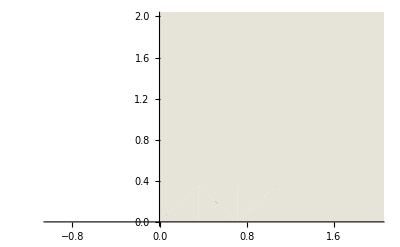

-Graphics-

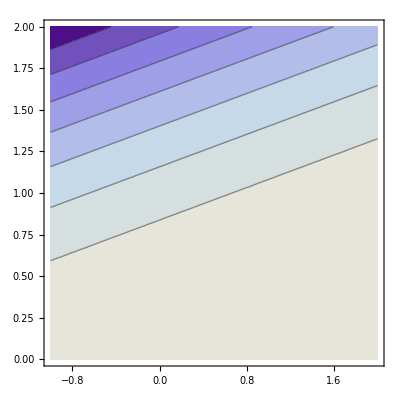

```mathematica
(* Singular Value Decomp on K=2 values with PERTURBED DATA *)

(* K VALUE *)
kSingularValues=2;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdPerturbedData42=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits42=FindFit[svdPerturbedData42,model,{a,b,c,d,e},{x,y}]

svdFitFun42=model/.svdFits42[[All]]

Show[
ListPlot[Tooltip[svdPerturbedData42[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun42,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdPerturbedData42[[All,1;;2]]]]
ContourPlot[svdFitFun42,{x,-1,2},{y,0,2}]
```

```mathematica
(* Singular Value Decomp on K=3 values with PERTURBED DATA *)

(* K VALUE *)
kSingularValues=3;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdPerturbedData43=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits43=FindFit[svdPerturbedData43,model,{a,b,c,d,e},{x,y}]

svdFitFun43=model/.svdFits43[[All]]

Show[
ListPlot[Tooltip[svdPerturbedData43[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun43,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdPerturbedData43[[All,1;;2]]]]
ContourPlot[svdFitFun43,{x,-1,2},{y,0,2}]
```

-Graphics-

{{0.150547,0.397878,1.01722,0.400509,0.999291},{0.104141,0.300022,0.945896,0.315401,1.00018},{0.0777844,0.238864,0.86869,0.26571,1.00066},{0.0508913,0.172655,0.764794,0.214041,1.00073},{0.0303591,0.120357,0.673827,0.174111,1.00023},{0.018581,0.080771,0.558573,0.14886,0.999719},{0.0140455,0.0537213,0.436535,0.136259,0.999361},{0.0131009,0.0318881,0.304582,0.129695,0.999134},{0.0177099,0.0186714,0.161058,0.132661,0.999711},{0.0240809,0.00817838,0.0139057,0.138694,1.00098}}

{{1.01722,0.400509,0},{0.945896,0.315401,0},{0.86869,0.26571,0},{0.764794,0.214041,0},{0.673827,0.174111,0},{0.558573,0.14886,0},{0.436535,0.136259,0},{0.304582,0.129695,0},{0.161058,0.132661,0},{0.0139057,0.138694,0}}

{a→-1.21724,b→-3.0337,c→0.922373,d→5.81538,e→-0.798388}

-0.798388+0.922373 x-x^2+5.81538 y-3.0337 x y-1.21724 y^2

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* Singular Value Decomp on K=4 values with PERTURBED DATA *)

(* K VALUE *)
kSingularValues=4;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdPerturbedData44=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits44=FindFit[svdPerturbedData44,model,{a,b,c,d,e},{x,y}]

svdFitFun44=model/.svdFits34[[All]]

Show[
ListPlot[Tooltip[svdPerturbedData44[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun44,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdPerturbedData44[[All,1;;2]]]]
ContourPlot[svdFitFun44,{x,-1,2},{y,0,2}]
```

-Graphics-

{{0.153781,0.40213,1.01681,0.394213,1.00006},{0.103067,0.298611,0.946034,0.317492,0.999922},{0.0748478,0.235003,0.869067,0.271427,0.99996},{0.0478608,0.168671,0.765183,0.219941,1.00002},{0.029562,0.119309,0.673929,0.175663,1.00004},{0.0199657,0.0825913,0.558396,0.146164,1.00005},{0.0167939,0.0573343,0.436183,0.130909,1.00001},{0.0165594,0.0364346,0.304139,0.122961,0.999952},{0.0187031,0.0199771,0.16093,0.130727,0.999947},{0.0201159,0.00296601,0.0144141,0.146414,1.00004}}

{{1.01681,0.394213,0},{0.946034,0.317492,0},{0.869067,0.271427,0},{0.765183,0.219941,0},{0.673929,0.175663,0},{0.558396,0.146164,0},{0.436183,0.130909,0},{0.304139,0.122961,0},{0.16093,0.130727,0},{0.0144141,0.146414,0}}

{a→-1.66907,b→-0.772686,c→0.684457,d→3.58171,e→-0.501524}

-0.501524+0.684457 x-x^2+3.58171 y-0.772686 x y-1.66907 y^2

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* Singular Value Decomp on K=5 values with PERTURBED DATA *)

(* K VALUE *)
kSingularValues=5;

{u2,w2,v2}=SingularValueDecomposition[newA,kSingularValues];

(* Significance value graph *)
ListPlot[Diagonal[w2]]

(* svd of orbit equation matrix *)
svdMatrix=u2.w2.Transpose[v2]

(* extracting x and y coords after svd *)
svdPerturbedData45=Table[{svdMatrix[[All,3]][[i]],svdMatrix[[All,4]][[i]],0},{i,1,10}]

(* Displaying new coordinate positions and predictive orbital plots *)
model=a*y^2+b*x*y+c*x+d*y+e-x^2;
svdFits45=FindFit[svdPerturbedData45,model,{a,b,c,d,e},{x,y}]

svdFitFun45=model/.svdFits45[[All]]

Show[
ListPlot[Tooltip[svdPerturbedData45[[All,1;;2]]],PlotRange->{{-1,2},{0,2}}],
ContourPlot[svdFitFun45,{x,0,20},{y,0,20}]
]
ListPlot[Tooltip[svdPerturbedData45[[All,1;;2]]]]
ContourPlot[svdFitFun45,{x,-1,2},{y,0,2}]
```

-Graphics-

{{0.155524,0.401055,1.01696,0.394365,1.},{0.100668,0.30009,0.945816,0.317282,1.},{0.073614,0.235764,0.868955,0.271319,1.},{0.0483947,0.168342,0.765231,0.219988,1.},{0.0308986,0.118485,0.67405,0.17578,1.},{0.0214007,0.0817065,0.558526,0.14629,1.},{0.0171451,0.0571177,0.436215,0.130939,1.},{0.0150879,0.0373419,0.304006,0.122833,1.},{0.0170519,0.0209952,0.160781,0.130583,1.},{0.0214717,0.00213012,0.0145369,0.146532,1.}}

{{1.01696,0.394365,0},{0.945816,0.317282,0},{0.868955,0.271319,0},{0.765231,0.219988,0},{0.67405,0.17578,0},{0.558526,0.14629,0},{0.436215,0.130939,0},{0.304006,0.122833,0},{0.160781,0.130583,0},{0.0145369,0.146532,0}}

{a→-1.74861,b→-0.712893,c→0.675912,d→3.56392,e→-0.497479}

-0.497479+0.675912 x-x^2+3.56392 y-0.712893 x y-1.74861 y^2

-Graphics-

-Graphics-

-Graphics-

```mathematica
Print["ORIGONAL DATA: a,b,c,d & e"]
svdFits31
svdFits32
svdFits33
svdFits34
svdFits35

Print["PERTURBED DATA: a,b,c,d & e"]
svdFits41
svdFits42
svdFits43
svdFits44
svdFits45
```

ORIGONAL DATA: a,b,c,d & e

{a→4.12807,b→1.43668,c→-7.36156×10^-16,d→-2.68472×10^-15,e→1.57988×10^-16}

{a→-2.63563,b→0.143646,c→0.551447,d→3.22294,e→-0.432894}

{a→-1.21724,b→-3.0337,c→0.922373,d→5.81538,e→-0.798388}

{a→-1.66907,b→-0.772686,c→0.684457,d→3.58171,e→-0.501524}

{a→-1.74861,b→-0.712893,c→0.675912,d→3.56392,e→-0.497479}

PERTURBED DATA: a,b,c,d & e

{a→4.12807,b→1.43668,c→-7.36156×10^-16,d→-2.68472×10^-15,e→1.57988×10^-16}

{a→-16.7679,b→8.18972,c→-0.534499,d→2.1887,e→-0.0714222}

{a→-1.21724,b→-3.0337,c→0.922373,d→5.81538,e→-0.798388}

{a→-1.66907,b→-0.772686,c→0.684457,d→3.58171,e→-0.501524}

{a→-1.74861,b→-0.712893,c→0.675912,d→3.56392,e→-0.497479}

```mathematica
(* Q: What effect does this difference have on the plots of the orbits? Can you explain this behavior? *)

(* A: The a,b,c,d and e's for the Origional you can see the data which takes all contributing parameters (k=5) is much more different than it's neighbor k=4 and k=3 is to k=2. That said, the total difference in all k values is not much because the data is consistant. However, for the perturbed data the differences between k=5 and k=4 is much more significant because the errors introduced to the system contribute MUCH more toward influencing the model. So by taking out some of the lowest contributing k values, we can reduce this very data senstitive system to look almost exactly like the origonal system. *)


(* Q: Which solution would you regard as better: one that fits the data more closely or one than is less sensitive to small perturbations in the data? Why? *)

(* A: In this particular case, I would regard the solution where the model is less sensitive to small perturbations to be superior because it represents the general behavior of the system even if the data collected is off by some small amount. I feel a model that is less sensitive to errors from data collection would provide a more trendingly accurate representation. A consistantly accureate model would be more benefitial for making predictions (like a trajectory model) than one that varies significantly from small deviations.
*)
```